```mathematica
d=3;
R=15;
l=12;
w=8;
g[x_]=0.5*(1+Cos[2*Pi/d*x]);
n[x_,y_]= Exp[-x^2/w^2-(y-R/5)^2/l^2];
```

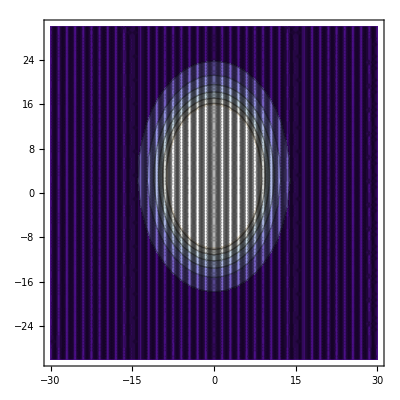

```mathematica
prison =ContourPlot[{g[x]},{x,-30,30},{y,-30,30},ContourShading->None];
nose = ContourPlot[{n[x,y]},{x,-30,30},{y,-30,30}];
Show[nose,prison]
```